```mathematica
(*Start with regular LP*)

targets={10,20,50,100,200,500,1000}
temptargets={2,5,10,20,50,100,200,500,1000}
extrapolate[sampsize_,popsize_,max_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];
If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];
b=mat[max,popsize];
bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};
sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}];
sol=LinearProgramming[c,bchp,N[Table[{sub[[1]][[1+i]],0},{i,1,sampsize}],100],Method->"RevisedSimplex"];
solmin=LinearProgramming[-c,bchp,N[Table[{sub[[1]][[1+i]],0},{i,1,sampsize}],200],Method->"RevisedSimplex"];
Return[{c.sol,c.solmin}]
]
```

{10,20,50,100,200,500,1000}

{2,5,10,20,50,100,200,500,1000}

```mathematica
N[res10]
```

{{843.388,843.388},{1035.03,1035.24},{1268.42,1312.62},{1373.84,1600.46},{1439.17,2082.75},{1486.56,3437.06},{1503.17,5660.22}}

```mathematica
N[res10]
```

{{843.388,843.388},Null,Null,Null,Null,Null,Null}

```mathematica
res10=N[Map[extrapolate[10,#,1000]&,targets]];
```

```mathematica
res20=Map[extrapolate[20,#,1000]&,targets];
```

{{100425876204301585269475900299670850120211366746401110126882666302904171365341647462784860865501293478156074002376437275984961079487730804497962520486326303087998145828709183944850489530023926601772925380275390114678681804922789656854508586126707478529259804893158224993754618271615396529398280568375938501982672221371782818614979877773851552165596642973943812376858904707401314670850337899428199164101818264275634588138301716125867637528690498340089527987958001154168681001710050756092440258926646068009318015539885863374077100886283168406189089705621945280835510743389721861364181769576342707810276385169732569497805056032894802501384220314749252421553414035155594790370623764831702959699171546021864155088340533877143605797028404834390947772151244830443811801351059206840362168360453727338696394872544324982374984974218803978110698361260130275928227455580138460274179654453562770000094051516063108247902665681286496305124125074140092705079003486038404242895575043097128653302169279170779893656809609910650272573356609210347130412147573793837456392180096475940639735854522625261822622397115077774979925673702121555134194658074915978647297128877605604998759843974777309782140666711750865381749423099224500669126512133381334159348557243722690362684339695233844455807309425982681493677203507673016080782363538039776268082761653655886861201997067967132575659360380679131087205491123486321158957051071898537140945370411932411327928466158137853633281801312017611534794781781574425926164125470405697618156820474488788534053830680945622042638477111203407660959225642981361874582289899652073644017441538339595785814381385133610529909348313339499927904190683373440436208309639328240611081245198340790191314403320507332846794055073584415417934951575000/119074286904892746177842748066392940159319261012095039124991744654627395427301557770759597531080342013632486265495401631911233657072506693079072205709306441414089804744860475944287243178264138129153485930711970295251394895183037262616847751232158277804895831888722318160400836540295571089614574983546196415022577677714072966974081444993433264990458824983263163042128422580547940662761264164000697944745923022401171223223487456181103729214283677814864196274054969871272159002198572218481213770009100348128446759725055867738373747341247466842818423936181188193291917888205117260418091597055728830572807511116884616610322370340744298487297601166690498190441791656479359094041960355948936575263374577954236372994647502005131648285927697867506874248284621969831105570199491337968336400010861145798453872040557266964336875799031731742198653996189593326955272433655574251417609312882526017289566512302014573285139462831601615654449682903026716416211457268668425995870736422668232629586614502230428832900794824012756662622936107506918541135522956432547750130338593311489403439680230666212834862422343299315348469499491145815903560105640585377544534627416568457817065787806868736442789708268867200136094361938350565205704654448372840526812392482908175800411880896485572135146351486029048449316994979745559869190323510759686587881072606681456287750094406399653598011376121584203996250038964493391241922439833066152119164040790204813929100355589979136225954786307354122254677903681060324273794038116137763642161764063994479587135261786381104189043556937183229707100981518953398323560483064467786437262121238250665320984273748228302590863475698021526184152580265313072643329139348390653784408476163728676607964832162476607185983463132629133566522846929,100425876204301585269475900299670850120211366746401110126882666302904171365341647462784860865501293478156074002376437275984961079487730804497962520486326303087998145828709183944850489530023926601772925380275390114678681804922789656854508586126707478529259804893158224993754618271615396529398280568375938501982672221371782818614979877773851552165596642973943812376858904707401314670850337899428199164101818264275634588138301716125867637528690498340089527987958001154168681001710050756092440258926646068009318015539885863374077100886283168406189089705621945280835510743389721861364181769576342707810276385169732569497805056032894802501384220314749252421553414035155594790370623764831702959699171546021864155088340533877143605797028404834390947772151244830443811801351059206840362168360453727338696394872544324982374984974218803978110698361260130275928227455580138460274179654453562770000094051516063108247902665681286496305124125074140092705079003486038404242895575043097128653302169279170779893656809609910650272573356609210347130412147573793837456392180096475940639735854522625261822622397115077774979925673702121555134194658074915978647297128877605604998759843974777309782140666711750865381749423099224500669126512133381334159348557243722690362684339695233844455807309425982681493677203507673016080782363538039776268082761653655886861201997067967132575659360380679131087205491123486321158957051071898537140945370411932411327928466158137853633281801312017611534794781781574425926164125470405697618156820474488788534053830680945622042638477111203407660959225642981361874582289899652073644017441538339595785814381385133610529909348313339499927904190683373440436208309639328240611081245198340790191314403320507332846794055073584415417934951575000/119074286904892746177842748066392940159319261012095039124991744654627395427301557770759597531080342013632486265495401631911233657072506693079072205709306441414089804744860475944287243178264138129153485930711970295251394895183037262616847751232158277804895831888722318160400836540295571089614574983546196415022577677714072966974081444993433264990458824983263163042128422580547940662761264164000697944745923022401171223223487456181103729214283677814864196274054969871272159002198572218481213770009100348128446759725055867738373747341247466842818423936181188193291917888205117260418091597055728830572807511116884616610322370340744298487297601166690498190441791656479359094041960355948936575263374577954236372994647502005131648285927697867506874248284621969831105570199491337968336400010861145798453872040557266964336875799031731742198653996189593326955272433655574251417609312882526017289566512302014573285139462831601615654449682903026716416211457268668425995870736422668232629586614502230428832900794824012756662622936107506918541135522956432547750130338593311489403439680230666212834862422343299315348469499491145815903560105640585377544534627416568457817065787806868736442789708268867200136094361938350565205704654448372840526812392482908175800411880896485572135146351486029048449316994979745559869190323510759686587881072606681456287750094406399653598011376121584203996250038964493391241922439833066152119164040790204813929100355589979136225954786307354122254677903681060324273794038116137763642161764063994479587135261786381104189043556937183229707100981518953398323560483064467786437262121238250665320984273748228302590863475698021526184152580265313072643329139348390653784408476163728676607964832162476607185983463132629133566522846929},{1035.12477460439935021454373284021552254168219778656849044351129698896310708507950841957181091258854,1035.12477460439935021454373284021552254168219778656849044351129698896310708507950841957181091258854},{1290.19000696366088167858160630695611394994816071604133784279655918884734428454534668623,1294.68039478011937247240070860944316486200420913719204431138829039497310391912650044185677},{1443.792023370116390692100177607348441774038270941079560485531544864858342823862025931,1517.987807005755192699912190853097039200262412772270419403440376861420554601266045602234},{1541.62994979523446393270302074921917905375721169270015997698339133987382226886239705,1833.241163495661460793536236035554093126689443650725197812858040822483879549973615989948},{1615.7229080593042519280188251132692306069601835091560991964550747287311224458,2641.8900815454182984510054141113038812876058318098045120463052962908044641746714159},{1643.537069961125365873467511583090579821928065853811597392491862766720375308738,3935.754256162109834325517669989572819298076191924642365610514555605343836751733}}

```mathematica
res100=Map[extrapolate[100,#,1000]&,targets];
```

$Aborted

```mathematica
N[res100[[7]]]
```

{0.,2116.41}

```mathematica
Export["~/Documents/capture_recapture/data/res10",res10,"TSV"]
Export["~/Documents/capture_recapture/data/res20",res20,"TSV"]
Export["~/Documents/capture_recapture/data/res40",res40,"TSV"]
Export["~/Documents/capture_recapture/data/res50",res50,"TSV"]
Export["~/Documents/capture_recapture/data/res1000",res1000,"TSV"]
```

~/Documents/capture_recapture/data/res10

~/Documents/capture_recapture/data/res20

~/Documents/capture_recapture/data/res40

~/Documents/capture_recapture/data/res50

~/Documents/capture_recapture/data/res1000

```mathematica
res1000=Map[extrapolate[1000,#,1000]&,targets];
```

```mathematica
N[res1000]
```

{{843.388,843.388},{1035.12,1035.12},{1292.27,1292.27},{1486.93,1486.93},{1680.06,1680.06},{1930.74,1930.74},{2115.18,2115.18}}

```mathematica
res50=Map[extrapolate[50,#,1000]&,targets];
```

```mathematica
scale=100/(5000-N[pop[[1,1]]])
```

0.0472773

{{3,1000},{25,250}}

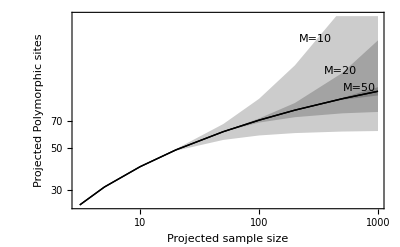

```mathematica
range={{3,1000},{25,250}}
Show[ListLogLogPlot[{Transpose[{targets,scale*res10[[1;;,1]]}],Transpose[{targets,scale*res10[[1;;,2]]}]},PlotRange->range,Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*res20[[1;;,1]]}],Transpose[{targets,scale*res20[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*res50[[1;;,1]]}],Transpose[{targets,scale*res50[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["M=10",{Log[300],Log[scale*4000]}],Inset["M=20",{Log[480],Log[scale*2700]}],Inset["M=50",{Log[700],Log[scale*2200]}]}]
```

```mathematica
(*Add the quadratic bounds!*)
(*The sup bound is linear*)
f[x_,extrap_,order_]:=Solve[{(1-x)^2-(1-x)^(extrap-order+2)==aa x(1-x)+bb x^2,-2(1-x)+(extrap-order+2)(1-x)^(extrap-order+1)==aa -2 aa x+2 bb x},{aa,bb}]

quadraticbound[sampsize_,popsize_,max_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=N[Transpose[Dot[bloc,Transpose[poploc]]]]; 
curr=Apply[Plus,sub[[1,2;;]]];
Return[{Max[Table[curr+aa/sampsize sub[[1,2]]+2 bb /(sampsize)/(sampsize+1)*sub[[1,3]]/.f[x,popsize,sampsize][[1]],{x,0.005,1,0.005}]],curr+sub[[1,2]]*(popsize-sampsize)/sampsize}]



]
```

```mathematica
quad10=Map[quadraticbound[10,#,1000]&,targets];
```

```mathematica
quad20=Map[quadraticbound[20,#,1000]&,targets];
```

```mathematica
quad50=Map[quadraticbound[50,#,1000]&,targets];
```

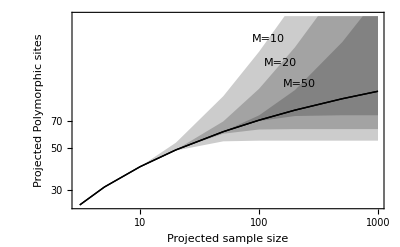

```mathematica
Show[ListLogLogPlot[{Transpose[{targets,scale*quad10[[1;;,1]]}],Transpose[{targets,scale*quad10[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray},PlotRange->range],

ListLogLogPlot[{Transpose[{targets,scale*quad20[[1;;,1]]}],Transpose[{targets,scale*quad20[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray},PlotRange->range],ListLogLogPlot[{Transpose[{targets,scale*quad50[[1;;,1]]}],Transpose[{targets,scale*quad50[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray},PlotRange->range],ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,Filling->{1->{2}},PlotStyle->{Black},PlotRange->range],Frame->{True,True,False,False},
FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["M=10",{Log[120],Log[scale*4000]}],Inset["M=20",{Log[150],Log[scale*3000]}],Inset["M=50",{Log[220],Log[scale*2300]}]}]
```

```mathematica
N[quad10]
N[quad20]
N[quad50]
N[res1000]
```

{{843.388,843.388},{1039.06,3715.08},{1198.6,12330.2},{1217.63,26688.7},{1218.12,55405.6},{1218.12,141556.},{1218.12,285141.}}

{{843.388,843.388},{1035.12,1035.12},{1131.04,9622.65},{1132.64,23935.2},{1132.64,52560.3},{1132.64,138435.},{1132.64,281561.}}

{{843.388,843.388},{1035.12,1035.12},{1292.27,1292.27},{1308.1,15498.5},{1308.1,43911.1},{1308.1,129149.},{1308.1,271211.}}

{{843.388,843.388},{1035.12,1035.12},{1292.27,1292.27},{1486.93,1486.93},{1680.06,1680.06},{1930.74,1930.74},{2115.18,2115.18}}

```mathematica
g[x_,Δ_]:=Solve[{(1-x)^3-(1-x)^(Δ+3)== Δ x(1-x)^2+bb x^2 (1-x)+cc x^3,-3(1-x)^2+(Δ+3)(1-x)^(Δ+2)==Δ(1-x)^2-2 x (1-x) Δ +2 bb x (1-x)-bb x^2+3 cc x^2},{bb,cc}]
cubicbound[sampsize_,popsize_,max_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=N[Transpose[Dot[bloc,Transpose[poploc]]]]; 
curr=Apply[Plus,sub[[1,2;;]]];
Return[{Max[Table[curr+aa/sampsize sub[[1,2]]+2 bb /(sampsize)/(sampsize+1)*sub[[1,3]]/.f[x,popsize,sampsize][[1]],{x,0.005,1,0.005}]],Min[Table[curr+(popsize-sampsize)/sampsize sub[[1,2]]+2 bb /(sampsize)/(sampsize+1)*sub[[1,3]]+6 cc /(sampsize)/(sampsize+1)/(sampsize+2)*sub[[1,4]]/.g[x,popsize-sampsize][[1]],{x,0.005,1,0.005}]]}]



]
```

```mathematica
cub10=Map[cubicbound[10,#,1000]&,targets];
```

```mathematica
cub20=Map[cubicbound[20,#,1000]&,targets];

cub50=Map[cubicbound[50,#,1000]&,targets];
```

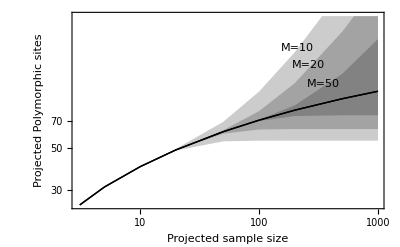

```mathematica
Show[ListLogLogPlot[{Transpose[{targets,scale*cub10[[1;;,1]]}],Transpose[{targets,scale*cub10[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray},PlotRange->range],

ListLogLogPlot[{Transpose[{targets,scale*cub20[[1;;,1]]}],Transpose[{targets,scale*cub20[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray},PlotRange->range],ListLogLogPlot[{Transpose[{targets,scale*cub50[[1;;,1]]}],Transpose[{targets,scale*cub50[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray},PlotRange->range],ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,Filling->{1->{2}},PlotStyle->{Black},PlotRange->range],Frame->{True,True,False,False},
FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["M=10",{Log[210],Log[scale*3600]}],Inset["M=20",{Log[260],Log[scale*2900]}],Inset["M=50",{Log[350],Log[scale*2300]}]}]
```

```mathematica
(*LinearProgramming with decreasing constraint*)

extrapolatemon[sampsize_,popsize_,max_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,popsize];


bloc=mat[popsize,sampsize];
(*projection matrix without singletons*)
bchp=bloc[[2;;,2;;]];
poploc=Transpose[Dot[b,Transpose[pop]]];
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
monotony=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->-1},{popsize,popsize}];
monotonconst=Table[{0,1},{it,1 popsize}];
c=Table[1,{i,1,popsize}];
mat1=Join[bchp,monotony];
vec1=Join[N[Table[{sub[[1]][[1+i]],0},{i,1,sampsize}],100],monotonconst];

sol=LinearProgramming[c,mat1,vec1,Method->"RevisedSimplex"];

solmin=LinearProgramming[-c,mat1,vec1,Method->"RevisedSimplex"];

Return[{c.sol,c.solmin}]



]
```

```mathematica
monot20=N[Map[extrapolatemon[20,#,1000]&,targets]];
monot50=N[Map[extrapolatemon[50,#,1000]&,targets]];
```

{10,20,50,100,200}

```mathematica
monot10=N[Map[extrapolatemon[10,#,1000]&,targets]];
```

$Aborted

```mathematica
N[monot10]
```

{{843.388,843.388},{1033.81,1036.46},{1260.92,1322.19},{1391.27,1625.82},{1476.85,2137.87}}

```mathematica
monot10
res10
```

{{843.388,843.388},{1033.81,1036.46},{1260.92,1322.19},{1391.27,1625.82},{1476.85,2137.87}}

{{843.388,843.388},{1035.03,1035.24},{1268.42,1312.62},{1373.84,1600.46},{1439.17,2082.75},{1486.56,3437.06},{1503.17,5660.22}}

```mathematica
targets
```

{10,20,50,100,200,500,1000}

```mathematica
extrapolatemon[10,50,1000]
```

{1260.924036569397317924200525253845362993203456670044868623529241816188617458876089307501,1322.185047047504223044071614621034119236407719361948061282841170044849090141822144744}

```mathematica
N[extrapolate[50,200,1000],10]
```

{1679.790228,1680.282662}

```mathematica
N[res50]
```

{{843.388,843.388},{1035.12,1035.12},{1292.27,1292.27},{1486.93,1486.93},{1679.79,1680.28},{1906.83,1950.89},{2009.18,2223.42}}

```mathematica
extrapolate[10,200,1000]
```

{1270.1259201530761633085901412481955921778165240808306620717094812360155709882683663406018583,2900.9130670114100267803972629527580870381965682348646780906432807431221578676375129590786983112967196166895714309062207096620106274210455452861033960147566926811117129612215159028472230223365}

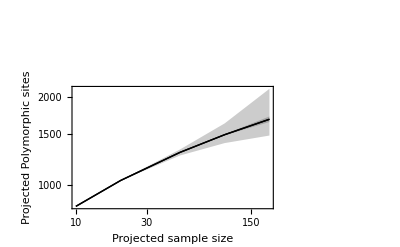

```mathematica
Show[ListLogLogPlot[{Transpose[{targets,monot10[[1;;,1]]}],Transpose[{targets,monot10[[1;;,2]]}]},Joined->True,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,monot20[[1;;,1]]}],Transpose[{targets,monot20[[1;;,2]]}]},Joined->True,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,monot50[[1;;,1]]}],Transpose[{targets,monot50[[1;;,2]]}]},Joined->True,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{temptargets,res1000[[1;;5,1]]}],Transpose[{temptargets,res1000[[1;;5,2]]}]},Joined->True,Filling->{1->{2}},PlotStyle->{Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["M=10",{Log[600],Log[4000]}],Inset["M=20",{Log[600],Log[3000]}],Inset["M=50",{Log[600],Log[2200]}]}]
```

```mathematica
(*Finally, extrapolate using the fact that the total population is 1000*)

extrapolateBest[sampsize_,popsize_,max_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[{tot,tot}];];


b=mat[max,sampsize];
bloc=mat[max,popsize];


(*projection matrix without singletons*)
bchp=b[[2;;,2;;]];
sub=Transpose[Dot[b,Transpose[pop]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)
c=Table[1,{i,1,popsize}].(bloc)[[2;;,2;;]];
sol=LinearProgramming[c,bchp,N[Table[{sub[[1]][[1+i]],0},{i,1,sampsize}],100],Method->"RevisedSimplex"];

solmin=LinearProgramming[-c,bchp,N[Table[{sub[[1]][[1+i]],0},{i,1,sampsize}],200],Method->"RevisedSimplex"];

Return[{c.sol,c.solmin}]



]
```

```mathematica
(*Obtain a direct Jackknife estimate*)
(*some definitions from test_general that apply independent of model*)

(*expansion in terms of delta to order o*)

d[t_,T_,o_]:=Sum[α[i] Δ[t,T]^i,{i,1,o}]
(*observed difference in counts in the last i individuals out of N_t. ve is the SFS*)
diff[Nt_,i_]:=Sum[Binomial[i,j]/Binomial[Nt,j]ve[j], {j,1,i}]

GenS[o_]:=Solve[Table[d[t-j,T,o]-d[t,T,o]==diff[t,j],{j,1,o}],Table[α[j],{j,1,o}]]

sPop [i_]:=Solve[Table[d[t-j,T,i]-d[t,T,i]==diff[t,j],{j,1,i}],Table[α[j],{j,1,i}]]/.Table[Δ[-k+t,T]-> Δ[t,T]+Sum[1/(j),{j,t,t+1-k,-1}],{k,1,i}]
δp[t1_,t2_]:=Sum[1/i,{i,t1+1,t2}]

jkPop[o_,vec_,pop_]:=Module[{samp},samp=Length[vec[[1]]]-1;N[Apply[Plus,vec[[1,2;;]]]+Sum[α[i]δp[samp,pop]^i,{i,1,o}]/.sPop[o]/.Δ[t,T]->δp[samp,pop]/.t->samp/.Table[ve[j]->vec[[1,1+j]],{j,1,o}]][[1]]]



extrapolatejkpop[sampsize_,popsize_,max_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[tot];];

If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[tot];];


b=mat[max,sampsize];
bloc=mat[max,popsize];


(*projection matrix without singletons*)
bchp=b[[2;;,2;;]];
sub=Transpose[Dot[b,Transpose[pop]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)

Return[jkPop[3,sub,popsize]]

]

sC[i_,f_]:=Solve[Table[d[t-j,T,i]-d[t,T,i]==diff[t,j],{j,1,i}],Table[α[j],{j,1,i}]]/.Table[Δ[-k+t,T]-> Δ[t,T]-(1-f)^t+(1-f)^(t-k),{k,1,i}]
jkCons[o_,vec_, pop_,ff_] := Module[{samp}, samp = Length[vec[[1]]] - 1;N[Apply[Plus, vec[[1, 2 ;;]]] + Sum[α[i] δc[samp , pop,ff]^i, {i, 1, o}] /. sC[o,ff] /. Δ[t,T] -> δc[samp , pop,ff] /. t -> samp /. Table[ve[j] -> vec[[1, 1 + j]], {j, 1, o}]][[1]]]

δc[t_,T_,f_]:=(1-f)^t-(1-f)^T

extrapolatejkcons[sampsize_,popsize_,max_,f_]:=Module[{b,bchp,tot},totsnp=5000;
pop={Table[10/(n+1/10),{n,0,max}]};
pop=pop/Apply[Plus,Flatten[pop]]*totsnp;
If[popsize==sampsize,(*Then project down rather than extrapolate.*)
bloc=mat[max,popsize];
poploc=pop;
sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[tot];];
If[popsize<sampsize,  (*Then project down rather than extrapolate.*)  b=mat[max,sampsize];
bchp=b[[2;;,2;;]];
bloc=mat[sampsize,popsize];
poploc=Transpose[Dot[b,Transpose[pop]]]; 

sub=Transpose[Dot[bloc,Transpose[poploc]]]; 
tot=Apply[Plus,sub[[1,2;;]]];
Return[tot];];


b=mat[max,sampsize];
bloc=mat[max,popsize];


(*projection matrix without singletons*)
bchp=b[[2;;,2;;]];
sub=Transpose[Dot[b,Transpose[pop]]];
 
(*pop={Table[10/(n+1/10),{n,0,popsize}]};

sub=Transpose[Dot[b,Transpose[pop]]];*)

Return[jkCons[3,sub,popsize,f]]

]
```

```mathematica
N[extrapolateBest[10,20,30]]
N[extrapolateBest[10,20,1000]]
```

{1250.56,1261.99}

{1034.35,1036.07}

```mathematica
N[extrapolate[10,20,30]]
N[extrapolate[10,20,1000]]
```

{1244.52,1269.67}

{1024.96,1045.47}

```mathematica
jkpop10=Map[extrapolatejkpop[10,#,1000]&,targets];
```

```mathematica
jkconsFp5T10=Map[extrapolatejkcons[10,#,1000,.5]&,targets];
```

```mathematica
jkconsFp1T10=Map[extrapolatejkcons[10,#,1000,.1]&,targets];
```

```mathematica
N[jkpop10]
N[jkconsFp5T10]
N[jkconsFp1T10]
N[res1000]
```

{{843.388,843.388},1035.13,1292.48,1487.79,1682.55,1938.18,2129.68}

{843.388,884.094,884.141,884.141,884.141,884.141,884.141}

{843.388,1026.17,1141.45,1147.04,1147.07,1147.07,1147.07}

{{432.328,432.328},{657.826,657.826},{843.388,843.388},{1035.12,1035.12},{1292.27,1292.27},{1486.93,1486.93},{1680.06,1680.06},{1930.74,1930.74},{2115.18,2115.18}}

```mathematica
targets
```

{10,20,50,100,200,500,1000}

```mathematica
best20=Map[extrapolateBest[20,#,1000]&,targets];
best50=Map[extrapolateBest[50,#,1000]&,targets];
```

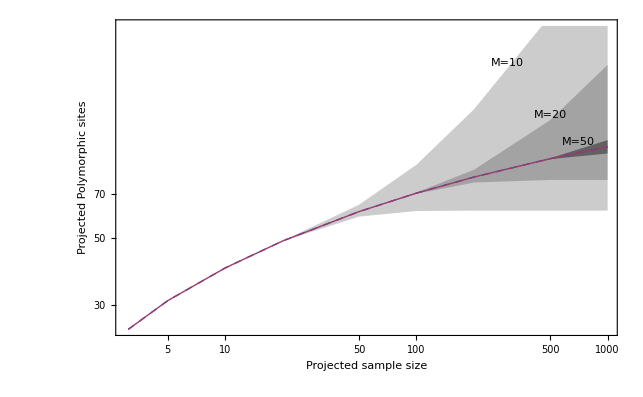

```mathematica
Show[ListLogLogPlot[{Transpose[{targets,scale*best10[[1;;,1]]}],Transpose[{targets,scale*best10[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*best20[[1;;,1]]}],Transpose[{targets,scale*best20[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*best50[[1;;,1]]}],Transpose[{targets,scale*best50[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.4],Gray}],
ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Dashed,Thin,Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["M=10",{Log[300],Log[scale*4000]}],Inset["M=20",{Log[500],Log[scale*2700]}],Inset["M=50",{Log[700],Log[scale*2200]}]}]
```

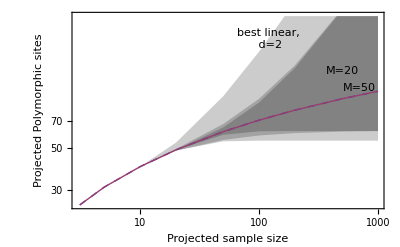

```mathematica
Show[ListLogLogPlot[{Transpose[{targets,scale*quad10[[1;;,1]]}],Transpose[{targets,scale*quad10[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*res10[[1;;,1]]}],Transpose[{targets,scale*res10[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*best10[[1;;,1]]}],Transpose[{targets,scale*best10[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Dashed,Thin,Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["best linear,\n d=2",{Log[120],Log[scale*4000]}],Inset["LP",{Log[500],Log[scale*2700]}],Inset["LP, N",{Log[700],Log[scale*2200]}]}]
```

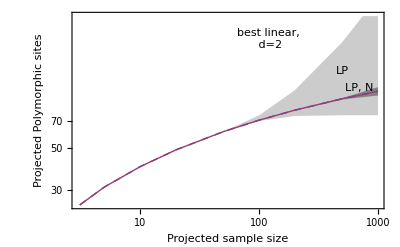

```mathematica
Show[ListLogLogPlot[{Transpose[{targets,scale*quad50[[1;;,1]]}],Transpose[{targets,scale*quad50[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*res50[[1;;,1]]}],Transpose[{targets,scale*res50[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{targets,scale*best50[[1;;,1]]}],Transpose[{targets,scale*best50[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2],Gray}],
ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Dashed,Thin,Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["best linear,\n d=2",{Log[120],Log[scale*4000]}],Inset["LP",{Log[500],Log[scale*2700]}],Inset["LP, N",{Log[700],Log[scale*2200]}]}]
```

```mathematica
Export["~/Documents/capture_recapture/data/cub10",cub10,"TSV"]
Export["~/Documents/capture_recapture/data/cub20",cub20,"TSV"]

Export["~/Documents/capture_recapture/data/cub50",cub50,"TSV"]
```

~/Documents/capture_recapture/data/cub10

~/Documents/capture_recapture/data/cub20

~/Documents/capture_recapture/data/cub50

{{5,1000},{30,250}}

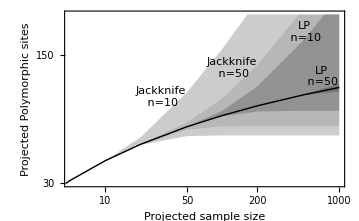

```mathematica
range={{5,1000},{30,250}}
Show[ListLogLogPlot[{Transpose[{targets,scale*quad10[[1;;,1]]}],Transpose[{targets,scale*quad10[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2]}],
ListLogLogPlot[{Transpose[{targets,scale*best10[[1;;,1]]}],Transpose[{targets,scale*best10[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.1]}],
ListLogLogPlot[{Transpose[{targets,scale*quad50[[1;;,1]]}],Transpose[{targets,scale*quad50[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2]}],
ListLogLogPlot[{Transpose[{targets,scale*best50[[1;;,1]]}],Transpose[{targets,scale*best50[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2]}],
ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Thickness[0.001],Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->{Inset["Jackknife\n n=10 ",{Log[30],Log[89]}],Inset["Jackknife\n n=50",{Log[120],Log[scale*2700]}],Inset["LP\n n=10",{Log[500],Log[200]}],Inset["LP\n n=50",{Log[700],Log[115]}]}]
```

{{5,1000},{30,250}}

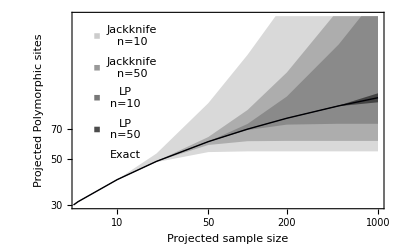

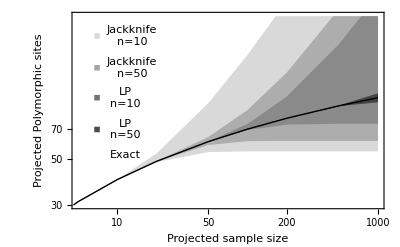

```mathematica
inset[pos_,name_,op_,off_]:={Inset[Graphics[{Black,Opacity[op],Rectangle[{0,0},{.1,.1}]}],{Log[7],Log[pos]},Automatic,0.5],Inset[Style[name,TextAlignment->Left],{Log[13-off],Log[pos]}]}

range={{5,1000},{30,250}}
Show[ListLogLogPlot[{Transpose[{targets,scale*quad10[[1;;,1]]}],Transpose[{targets,scale*quad10[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.15]}],
ListLogLogPlot[{Transpose[{targets,scale*best10[[1;;,1]]}],Transpose[{targets,scale*best10[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.2]}],
ListLogLogPlot[{Transpose[{targets,scale*quad50[[1;;,1]]}],Transpose[{targets,scale*quad50[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Opacity[0]},Filling->{1->{2}},FillingStyle->{Opacity[0.2]}],
ListLogLogPlot[{Transpose[{targets,scale*best50[[1;;,1]]}],Transpose[{targets,scale*best50[[1;;,2]]}]},Joined->True,PlotRange->range,Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->{Opacity[0.5]}],
ListLogLogPlot[{Transpose[{temptargets,scale*res1000[[1;;,1]]}],Transpose[{temptargets,scale*res1000[[1;;,2]]}]},Joined->True,PlotRange->range,PlotStyle->{Thickness[0.001] ,Black}],Frame->{True,True,False,False},FrameLabel->{"Projected sample size","Projected Polymorphic sites"},Epilog->Join[inset[200,"Jackknife\nn=10",.2,0],inset[140,"Jackknife\nn=50",.4,0],inset[100,"LP\nn=10",0.53,1.5],inset[70,"LP\nn=50",.7,1.5] ,{Inset[Graphics[{Thick,Black,Line[{{0,0},{1,0}}]}],{Log[7],Log[52]},Automatic,.5],Inset[Style["Exact",TextAlignment->Left],{Log[13-1.5],Log[52.5]}]}]]
```

```mathematica
scale*N[res1000][[6]]
scale*quad10[[4]]
scale*quad20[[4]]
scale*quad50[[4]]


scale*cub10[[4]]
scale*cub20[[4]]
scale*cub50[[4]]

Print["LP"]
scale*res10[[4]]
scale*res20[[4]]
scale*res50[[4]]
Print["Best"]
scale*best10[[4]]
scale*best20[[4]]
scale*best50[[4]]

scale2=100/79.42854345159607
Print["N=200"]
scale2 scale*N[res1000][[7]]
Print["d=2"]
scale2 scale*quad10[[5]]
scale2 scale*quad20[[5]]
scale2 scale*quad50[[5]]

Print["d=2,3"]
scale2*scale*cub10[[5]]
scale2*scale*cub20[[5]]
scale2*scale*cub50[[5]]

Print["LP"]
scale2*scale*res10[[5]]
scale2*scale*res20[[5]]
scale2*scale*res50[[5]]
Print["Best"]
scale2*scale*best10[[5]]
scale2*scale*best20[[5]]
scale2*scale*best50[[5]]
```

{70.2981,70.2981}

{54.7433,162.062}

{62.7269,103.071}

{69.5681,74.5278}

{54.7433,99.6751}

{62.7269,78.4916}

{69.5681,70.6659}

LP

{58.3266,91.2287}

{68.2586,71.7663}

{70.2981,70.2981}

Best

{61.3753,87.194}

{70.0097,70.6431}

{70.2981,70.2981}

1.25899

N=200

{100.,100.}

d=2

{68.9286,374.964}

{79.3887,214.956}

{93.0761,127.653}

d=2,3

{68.9286,202.919}

{79.3887,139.187}

{93.0761,106.107}

LP

{75.6001,172.667}

{91.7605,109.118}

{99.9841,100.013}

Best

{77.517,167.229}

{95.9215,105.71}

1001